```mathematica
Laplacian[f[x,t], {x}]
```

f^(2,0)[x,t]

```mathematica
Laplacian[f[x,y], {x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
With[{f=√(1-#1^2-#2^2)&},
Laplacian[f[x,y], {x,y}]]
```

-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))

```mathematica
Simplify[-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))]
```

(-2+x^2+y^2)/((1-x^2-y^2)^(3/2))

```mathematica
Plot3D[(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
With[{a=1},
Plot3D[(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),{x,-a,a},{y,-a,a}]]
```

-Graphics3D-

```mathematica
∫_a^b Sin[1/x]ⅆx
```

ConditionalExpression[CosIntegral[1/a]-CosIntegral[1/b]-a Sin[1/a]+b Sin[1/b],((Re[b]<0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[b]<Im[a]<0||(a∈ℝ&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>(Im[a] Re[b])/Im[b])))||(b∈ℝ&&(Im[a]<0||(a∈ℝ&&(Re[a]<Re[b]||Re[b]<Re[a]<Re[b]/2+1/2 √(Re[b]^2)))||Im[a]>0))||(Im[b]>0&&((Im[a]<0&&Re[a]>(Im[a] Re[b])/Im[b])||(a∈ℝ&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[a]>Im[b]))))||(Re[b]==0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<0||Re[a]>0))||Im[b]<Im[a]<0||(a∈ℝ&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>0)))||(Im[b]>0&&((Im[a]<0&&Re[a]>0)||(a∈ℝ&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<0||Re[a]>0))||Im[a]>Im[b]))))||(Re[b]>0&&((Im[b]<0&&(Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[b]<Im[a]<0||(a∈ℝ&&(Re[a]<0||Re[a]>0))||(Im[a]>0&&Re[a]>(Im[a] Re[b])/Im[b])))||(b∈ℝ&&(Im[a]<0||(a∈ℝ&&(Re[b]/2-1/2 √(Re[b]^2)<Re[a]<Re[b]||Re[a]>Re[b]))||Im[a]>0))||(Im[b]>0&&((Im[a]<0&&Re[a]>(Im[a] Re[b])/Im[b])||(a∈ℝ&&(Re[a]<0||Re[a]>0))||0<Im[a]<Im[b]||(Im[a]==Im[b]&&(Re[a]<(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]||Re[a]>(-Im[a] Im[b]+Im[b]^2+Re[b]^2)/Re[b]))||Im[a]>Im[b])))))&&((a/(a-b)≠0&&Re[a/(-a+b)]≥0)||Im[a/(-a+b)]≠0||Re[a/(a-b)]>1)&&((Im[a]≥0&&Re[a/(a-b)]≥1&&Im[a]≤Im[b])||(Im[a]≥0&&Re[a/(-a+b)]≥0&&Im[a]≤Im[b])||(Im[a]≥0&&Im[a]≤Im[b]&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Im[b]≥0&&Re[a/(a-b)]≥1)||(Im[a]≥Im[b]&&Im[b]≥0&&Re[a/(-a+b)]≥0)||(Im[a]≥Im[b]&&Im[b]≥0&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Re[a/(a-b)]≥1&&Im[a]≤0)||(Im[a]≥Im[b]&&Re[a/(a-b)]≥1&&Im[b] Re[a]≤Im[a] Re[b])||(Im[a]≥Im[b]&&Re[a/(-a+b)]≥0&&Im[a]≤0)||(Im[a]≥Im[b]&&Re[a/(-a+b)]≥0&&Im[b] Re[a]≤Im[a] Re[b])||(Im[a]≥Im[b]&&Im[a]≤0&&Im[a/(-a+b)]≠0)||(Im[a]≥Im[b]&&Im[b] Re[a]≤Im[a] Re[b]&&Im[a/(-a+b)]≠0)||(Im[b] Re[a]≥Im[a] Re[b]&&Re[a/(a-b)]≥1&&Im[a]≤Im[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Re[a/(-a+b)]≥0&&Im[a]≤Im[b])||(Im[b] Re[a]≥Im[a] Re[b]&&Im[a]≤Im[b]&&Im[a/(-a+b)]≠0)||(Re[a/(a-b)]≥1&&Im[a]≤Im[b]&&Im[b]≤0)||(Re[a/(-a+b)]≥0&&Im[a]≤Im[b]&&Im[b]≤0)||(Im[a]≤Im[b]&&Im[b]≤0&&Im[a/(-a+b)]≠0))]

```mathematica
FullSimplify[
∫_a^b Sin[1/x]ⅆx, {a,b,x}∈Reals]
```

ConditionalExpression[CosIntegral[1/a]-CosIntegral[1/b]-a Sin[1/a]+b Sin[1/b],((b<0&&(a<b||(a<0&&a>b)))||(b>0&&(a>b||(a>0&&a<b))))&&(a Im[1/(-a+b)]≠0||a Re[1/(a-b)]>1||a^2<a b)]

```mathematica
With[{limit=4},
Plot3D[
CosIntegral[1/a]-CosIntegral[1/b]-a Sin[1/a]+b Sin[1/b],
{a, -limit, limit}, {b, -limit,limit}]]
```

-Graphics3D-

```mathematica
With[{limit=4},
Plot3D[
CosIntegral[1/a]-CosIntegral[1/b]-a Sin[1/a]+b Sin[1/b],
{a, -limit, limit}, {b, -limit,limit}, AxesLabel->{a, b}]]
```

-Graphics3D-

```mathematica
With[{limit=1},
Plot3D[
CosIntegral[1/a]-CosIntegral[1/b]-a Sin[1/a]+b Sin[1/b],
{a, -limit, limit}, {b, -limit,limit}, AxesLabel->{a, b}]]
```

-Graphics3D-

```mathematica
Expectation[NormalDistribution[]]
```

Expectation::argmu: Expectation called with 1 argument; 2 or more arguments are expected.

Expectation[NormalDistribution[0,1]]

```mathematica
Expectation[x, NormalDistribution[]]
```

Expectation[x,NormalDistribution[0,1]]

```mathematica
Expectation[x, x\[Distributed]NormalDistribution[]]
```

0

```mathematica
Expectation[x, x\[Distributed]NormalDistribution[]]
```

```mathematica
Expectation[2x, x\[Distributed]NormalDistribution[1, 1]]
```

2

```mathematica
Expectation[x^2, x\[Distributed]NormalDistribution[1, 1]]
```

2

```mathematica
Expectation[Exp[x], x\[Distributed]NormalDistribution[1, 1]]
```

ⅇ^(3/2)

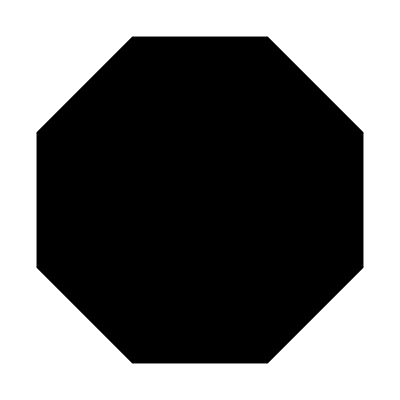

```mathematica
RegularPolygon[8] // Graphics
```

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
FullForm[Circle[]]
```

Circle[List[0,0]]

```mathematica
FullForm[NormalDistribution[]]
```

NormalDistribution[0,1]

```mathematica
Hold[1+1]
```

Hold[1+1]

```mathematica
FullForm[Hold[1+1]]
```

Hold[Plus[1,1]]

```mathematica
ReleaseHold[Hold[1+1]]
```

2

```mathematica
Hold[Hold[1+1]]
```

Hold[Hold[1+1]]

```mathematica
1+Hold[1+1]
```

1+Hold[1+1]

```mathematica
ReleaseHold[1+Hold[1+1]]
```

3

```mathematica
FullForm[1+Hold[1+1]]
```

Plus[1,Hold[Plus[1,1]]]

```mathematica
MapAt[Evaluate,1+Hold[1+1],2]
```

1+Hold[1+1]

```mathematica
Laplacian[f[x],x]
```

f[x]x

```mathematica
Laplacian[f[x,y],x]
```

f[x,y]x

```mathematica
Laplacian[f[x,y],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
∫f''[x]ⅆx
```

f'[x]

```mathematica
∫f'[x]ⅆx
```

f[x]

```mathematica
∫f[x]ⅆx
```

∫f[x]ⅆx

```mathematica
Laplacian[f[x],{x}]
```

f''[x]

```mathematica
Laplacian[√(1-x^2-y^2),{x,y}]
```

-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))

```mathematica
Simplify[-x^2/((1-x^2-y^2)^(3/2))-y^2/((1-x^2-y^2)^(3/2))-2/(√(1-x^2-y^2))]
```

(-2+x^2+y^2)/((1-x^2-y^2)^(3/2))

```mathematica
Plot3D[
(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),
{x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
Plot3D[
(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),
{x, -1, 1}, {y, -1, 1}]
```

-Graphics3D-

```mathematica
Plot3D[
(-2+x^2+y^2)/((1-x^2-y^2)^(3/2)),
{x,y}∈Disk[{0,0},1]]
```

Power::infy: Infinite expression 1/0. encountered.

-Graphics3D-

```mathematica
Grad[√(1-x^2-y^2), {x,y}]
```

{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}

```mathematica
Grad[√(1-x^2-y^2), {x,y}]
```

```mathematica
VectorPlot3D[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,y}∈Disk[{0,0},1]]
```

VectorPlot3D::idomdim: {x,y}∈Disk[{0,0},1] does not have a valid dimension as a plotting domain.

VectorPlot3D[{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))},{x,y}∈Disk[{0,0},1]]

```mathematica
VectorPlot3D[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,-1,1},{y,-1,1}]
```

VectorPlot3D::argrx: VectorPlot3D called with 3 arguments; 4 arguments are expected.

VectorPlot3D[{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))},{x,-1,1},{y,-1,1}]

```mathematica
VectorPlot3D[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,-1,1},{y,-1,1}, {z,-2,2}]
```

-Graphics3D-

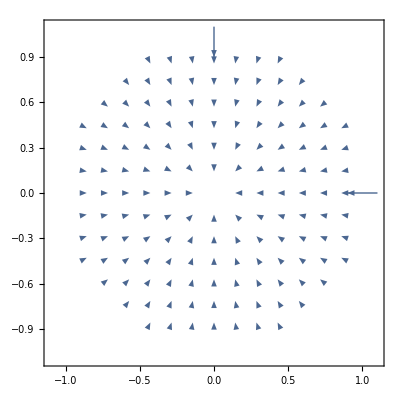

```mathematica
VectorPlot[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,-1,1},{y,-1,1}]
```

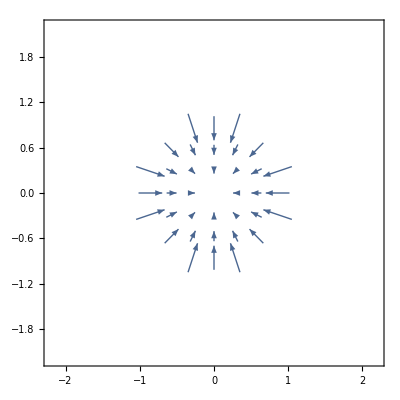

```mathematica
VectorPlot[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,-2,2},{y,-2,2}]
```

```mathematica
Grad[f[x,y,z],{x,y,z}]
```

{f^(1,0,0)[x,y,z],f^(0,1,0)[x,y,z],f^(0,0,1)[x,y,z]}

```mathematica
Solve[{Derivative[1,0,0][f][x,y,z]==0,Derivative[0,1,0][f][x,y,z]==0,Derivative[0,0,1][f][x,y,z]==0},{x,y,z}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{f^(1,0,0)[x,y,z]==0,f^(0,1,0)[x,y,z]==0,f^(0,0,1)[x,y,z]==0},{x,y,z}]

```mathematica
Grad[f[r,θ,z],{r,θ,z},"Cylindrical"]
```

{f^(1,0,0)[r,θ,z],(f^(0,1,0)[r,θ,z])/r,f^(0,0,1)[r,θ,z]}

```mathematica
Grad[√(1-x^2-y^2),{x,y}]
```

{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}

```mathematica
Solve[{-x/(√(1-x^2-y^2))==0,-y/(√(1-x^2-y^2))==0}, {x,y}]
```

{{x→0,y→0}}

```mathematica
∇_x f[x]
```

f[x]x

```mathematica
∇_{x,y} f[x,y]
```

{f^(1,0)[x,y],f^(0,1)[x,y]}

```mathematica
f[x]==x
```

f[x]==x

```mathematica
x==r Cos[θ]
```

x==r Cos[θ]

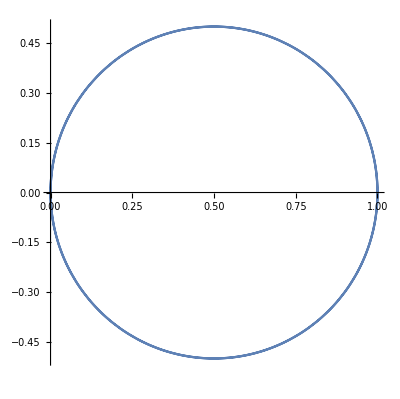

```mathematica
PolarPlot[Cos[θ], {θ, 0, 2π}]
```

```mathematica
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}
```

{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
∇
```

```mathematica
Plot3D[Sin[x y],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[{0,0},2]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
VectorPlot[
{-x/(√(1-x^2-y^2)),-y/(√(1-x^2-y^2))}, {x,-2,2},{y,-2,2}]
```

```mathematica
Grad[Sin[x y], {x,y}]
```

{y Cos[x y],x Cos[x y]}

```mathematica
Solve[{y Cos[x y]==0,x Cos[x y]==0},{x,y}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is ArcCos[Cos[x y]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[x y]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0,y→0}}

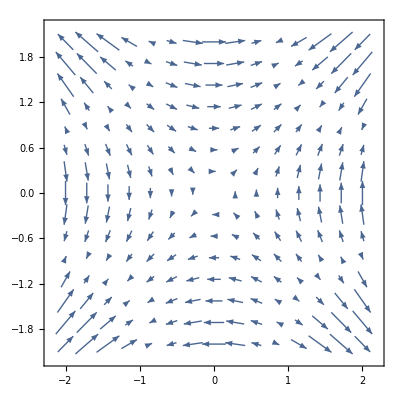

```mathematica
VectorPlot[
{y Cos[x y],x Cos[x y]},
 {x,-2,2},{y,-2,2}]
```

```mathematica
θ''[t]==μ θ'[t]-g/L Sin[θ[t]]
```

θ''[t]==-(g Sin[θ[t]])/L+μ θ'[t]

```mathematica
DSolve[θ''[t]==-(g Sin[θ[t]])/L+μ θ'[t],{θ[t],θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[θ''[t]==-(g Sin[θ[t]])/L+μ θ'[t],{θ[t],θ[t]},{t}]

```mathematica
θ''[t]==-μ θ'[t]+g/L Sin[θ[t]]
```

θ''[t]==(g Sin[θ[t]])/L-μ θ'[t]

```mathematica
DSolve[θ''[t]==(g Sin[θ[t]])/L-μ θ'[t],{θ[t],θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[θ''[t]==(g Sin[θ[t]])/L-μ θ'[t],{θ[t],θ[t]},{t}]

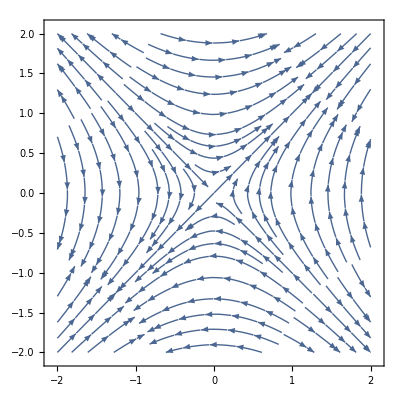

```mathematica
StreamPlot[
{y Cos[x y],x Cos[x y]},
 {x,-2,2},{y,-2,2}]
```

```mathematica
StreamPlot[
{y Cos[x y],x Cos[x y]},
 {x,-2,2},{y,-2,2}, ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
θ''[t]==g/L Sin[θ[t]]
```

θ''[t]==(g Sin[θ[t]])/L

```mathematica
DSolve[θ''[t]==(g Sin[θ[t]])/L,{θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 JacobiAmplitude[(ⅈ √(2 g-L C[1]) (t+C[2]))/(2 √L),(4 g)/(2 g-L C[1])]},{θ[t]→-2 JacobiAmplitude[(ⅈ t √(2 g-L C[1]))/(2 √L)+(ⅈ √(2 g-L C[1]) C[2])/(2 √L),(4 g)/(2 g-L C[1])]}}

```mathematica
θ''[t]==-(g Sin[θ[t]])/L
```

θ''[t]==-(g Sin[θ[t]])/L

```mathematica
DSolve[θ''[t]==-(g Sin[θ[t]])/L,{θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→2 JacobiAmplitude[(√(2 g+L C[1]) (t+C[2]))/(2 √L),(4 g)/(2 g+L C[1])]},{θ[t]→-2 JacobiAmplitude[(t √(2 g+L C[1]))/(2 √L)+(√(2 g+L C[1]) C[2])/(2 √L),(4 g)/(2 g+L C[1])]}}

```mathematica
2 JacobiAmplitude[(√(2 g+L) (t))/(2 √L),(4 g)/(2 g+L)]
```

2 JacobiAmplitude[(√(2 g+L) t)/(2 √L),(4 g)/(2 g+L)]

```mathematica
Manipulate[Plot[2 JacobiAmplitude[(√(2 g+L) t)/(2 √L),(4 g)/(2 g+L)],{t,-8,8}],{g,-8,8},{L,-2,2}]
```

```mathematica
Manipulate[Plot[2 JacobiAmplitude[(√(2 g+L) t)/(2 √L),(4 g)/(2 g+L)],{t,-8,8}],{g,-8,8},{L,-2,2}]
```

```mathematica
θ''[t]==-μ θ'[t]+9.8Sin[θ[t]]
```

θ''[t]==9.8 Sin[θ[t]]-μ θ'[t]

```mathematica
θ''[t]==- θ'[t]+9.8Sin[θ[t]]
```

θ''[t]==9.8 Sin[θ[t]]-θ'[t]

```mathematica
DSolve[θ''[t]==9.8 Sin[θ[t]]-θ'[t],{θ[t],θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[θ''[t]==9.8 Sin[θ[t]]-θ'[t],{θ[t],θ[t]},{t}]

```mathematica
θ''[t]==9.8Sin[θ[t]]
```

θ''[t]==9.8 Sin[θ[t]]

```mathematica
DSolve[θ''[t]==9.8 Sin[θ[t]],{θ[t]},{t}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ[t]→-2. JacobiAmplitude[0.5 √(-19.6 t^2+t^2 C[1]-39.2 t C[2]+2. t C[1] C[2]-19.6 C[2]^2+C[1] C[2]^2),-39.2/(-19.6+C[1])]},{θ[t]→2. JacobiAmplitude[0.5 √(-19.6 t^2+t^2 C[1]-39.2 t C[2]+2. t C[1] C[2]-19.6 C[2]^2+C[1] C[2]^2),-39.2/(-19.6+C[1])]}}

```mathematica
2. JacobiAmplitude[0.5 √(-19.6 t^2+t^2 C[1]-39.2 t C[2]+2. t C[1] C[2]-19.6 C[2]^2+C[1] C[2]^2),-39.2/(-19.6+C[1])]
```

2. JacobiAmplitude[0.5 √(-19.6 t^2+t^2 C[1]-39.2 t C[2]+2. t C[1] C[2]-19.6 C[2]^2+C[1] C[2]^2),-39.2/(-19.6+C[1])]

```mathematica
Simplify[2. JacobiAmplitude[0.5 √(-19.6 t^2+t^2 C[1]-39.2 t C[2]+2. t C[1] C[2]-19.6 C[2]^2+C[1] C[2]^2),-39.2/(-19.6+C[1])]]
```

2. JacobiAmplitude[0.5 √(t^2 (-19.6+C[1])+t (-39.2+2. C[1]) C[2]+(-19.6+C[1]) C[2]^2),-39.2/(-19.6+C[1])]

```mathematica
2. JacobiAmplitude[0.5 √(t^2 (-19.6`+1)+t (-39.2+2.)+(-19.6`+1)),-39.2/(-19.6+ 1)]
```

2. JacobiAmplitude[0.5 √(-20.-37.2 t-20. t^2),2.10753]

```mathematica
FullSimplify[2. JacobiAmplitude[0.5 √(-19.6`1.-37.2 t-19.6`1. t^2),2.10752688172043]]
```

2. JacobiAmplitude[0.5 √(-20.+(-37.2-19.6 t) t),2.10753]

```mathematica
Plot[
2. JacobiAmplitude[0.5 √(-19.6`1.+(-37.2-19.6 t) t),2.10752688172043], {t, -2, 2}]
```

-Graphics-

```mathematica
Cos[x]
```

Cos[x]

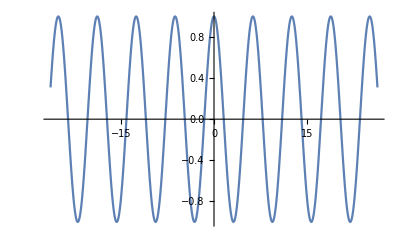

```mathematica
Plot[Cos[x],{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Information[Cos]
```

Cos[z] gives the cosine of z.

Attributes[Cos]={Listable,NumericFunction,Protected}

```mathematica
Cos[θ]/2
```

Cos[θ]/2

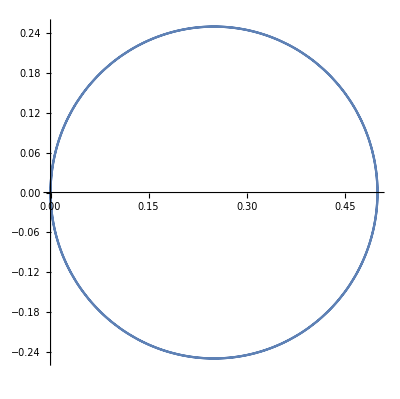

```mathematica
PolarPlot[Cos[θ]/2,{θ,0,2 π}]
```

```mathematica
Cos[x]/2
```

Cos[x]/2

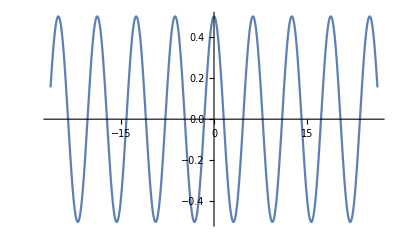

```mathematica
Plot[Cos[x]/2,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
1/2+Cos[x]/2
```

1/2+Cos[x]/2

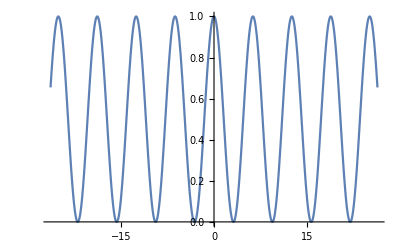

```mathematica
Plot[1/2+Cos[x]/2,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
(1+Cos[x])/2
```

1/2 (1+Cos[x])

```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])

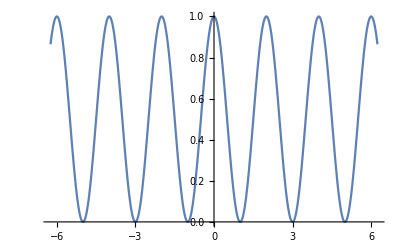

```mathematica
Plot[1/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
(1-(1+Cos[π x])/2)f[x]+(1+Cos[π x])/2 g[x]
```

(1+1/2 (-1-Cos[π x])) f[x]+1/2 (1+Cos[π x]) g[x]

```mathematica
FullSimplify[(1+1/2 (-1-Cos[π x])) f[x]+1/2 (1+Cos[π x]) g[x]]
```

1/2 (f[x]+g[x]+Cos[π x] (-f[x]+g[x]))

```mathematica
(1-(1+Cos[π x])/2)x+(1+Cos[π x])/2(2x)
```

x (1+1/2 (-1-Cos[π x]))+x (1+Cos[π x])

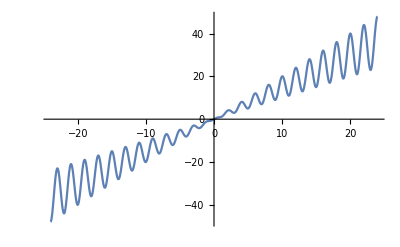

```mathematica
Plot[x (1+1/2 (-1-Cos[π x]))+x (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
NormalDistribution[]
```

NormalDistribution[0,1]

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

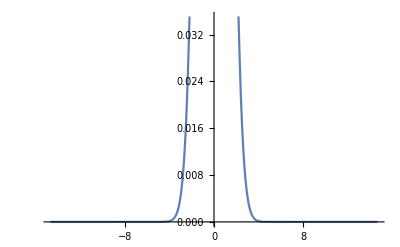

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-14.696938456699069,14.696938456699069}]
```

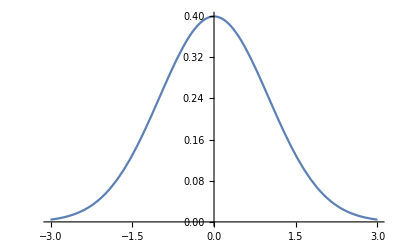

```mathematica
Plot[(ⅇ^(-x^2/2))/(√(2 π)),{x,-3,3}]
```

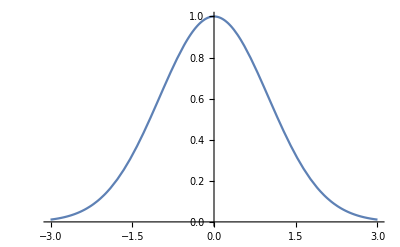

```mathematica
Plot[ⅇ^(-x^2/2),{x,-3,3}]
```

```mathematica
x^3(ⅇ^(-x^2/2))+x
```

x+ⅇ^(-x^2/2) x^3

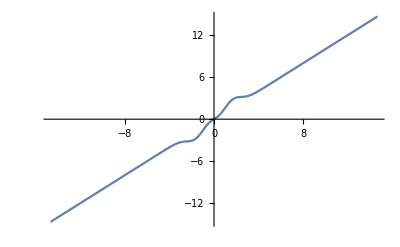

```mathematica
Plot[x+ⅇ^(-x^2/2) x^3,{x,-14.696938456699069,14.696938456699069}]
```

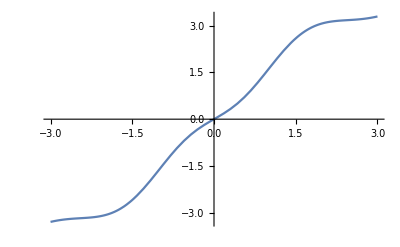

```mathematica
Plot[x+ⅇ^(-x^2/2) x^3,{x,-3,3}]
```

```mathematica
x^3
```

x^3

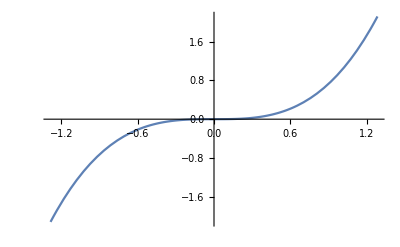

```mathematica
Plot[x^3,{x,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
x^3(ⅇ^(-x^2/2))+x(1-(ⅇ^(-x^2/2)))
```

(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3

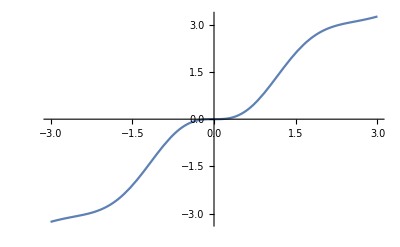

```mathematica
Plot[(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3,{x,-3,3}]
```

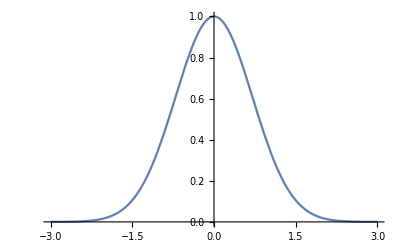

```mathematica
Plot[ⅇ^(-x^2),{x,-3,3}]
```

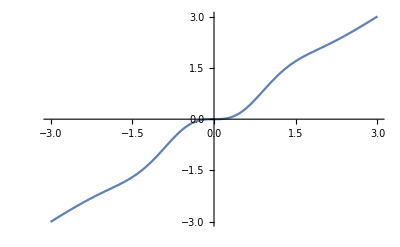

```mathematica
Plot[(1-ⅇ^(-x^2)) x+ⅇ^(-x^2) x^3,{x,-3,3}]
```

```mathematica
(1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3
```

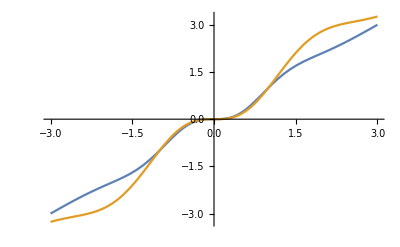

```mathematica
Plot[{(1-ⅇ^(-x^2)) x+ⅇ^(-x^2) x^3, (1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3},{x,-3,3}]
```

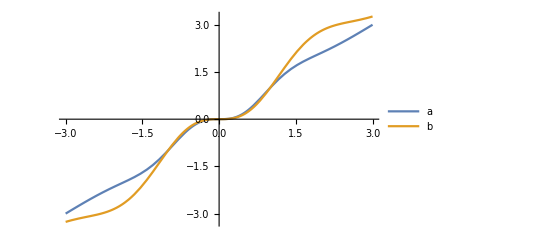

```mathematica
Plot[{(1-ⅇ^(-x^2)) x+ⅇ^(-x^2) x^3, (1-ⅇ^(-x^2/2)) x+ⅇ^(-x^2/2) x^3},{x,-3,3}, PlotLegends->{a,b}]
```

```mathematica
Plot3D[x (1+1/2 (-1-Cos[π x]))+x (1+Cos[π x]),{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Plot3D[x (1+1/2 (-1-Cos[π x]))+x (1+Cos[π x]),{x,y}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
Plot3D[x (1+1/2 (-1-Cos[π x y]))+x (1+Cos[π x]),{x,y}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
Plot3D[x (1+1/2 (-1-Cos[π x y]))+x (1+Cos[π x]),{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Grad[x (1+1/2 (-1-Cos[π x y]))+x (1+Cos[π x]), {x,y}]
```

{2+Cos[π x]+1/2 (-1-Cos[π x y])-π x Sin[π x]+1/2 π x y Sin[π x y],1/2 π x^2 Sin[π x y]}

```mathematica
Solve[{2+Cos[π x]+1/2 (-1-Cos[π x y])-π x Sin[π x]+1/2 π x y Sin[π x y]==0,1/2 π x^2 Sin[π x y]==0},{x,y}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{2+Cos[π x]+1/2 (-1-Cos[π x y])-π x Sin[π x]+1/2 π x y Sin[π x y]==0,1/2 π x^2 Sin[π x y]==0},{x,y}]

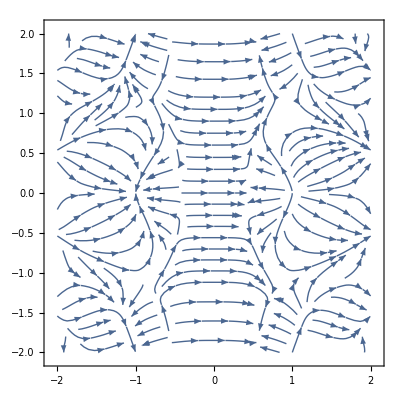

```mathematica
StreamPlot[
{2+Cos[π x]+1/2 (-1-Cos[π x y])-π x Sin[π x]+1/2 π x y Sin[π x y],1/2 π x^2 Sin[π x y]},
{x,-2,2},{y,-2,2}]
```

```mathematica
Laplacian[x (1+1/2 (-1-Cos[π x y]))+x (1+Cos[π x]), {x,y}]
```

-π^2 x Cos[π x]+1/2 π^2 x^3 Cos[π x y]+1/2 π^2 x y^2 Cos[π x y]-2 π Sin[π x]+π y Sin[π x y]

```mathematica
Plot3D[-π^2 x Cos[π x]+1/2 π^2 x^3 Cos[π x y]+1/2 π^2 x y^2 Cos[π x y]-2 π Sin[π x]+π y Sin[π x y],{x,-2.4687927747015435,13.689252681297166},{y,-2.771906616237416,92.0938648634691}]
```

-Graphics3D-

```mathematica
Plot3D[-π^2 x Cos[π x]+1/2 π^2 x^3 Cos[π x y]+1/2 π^2 x y^2 Cos[π x y]-2 π Sin[π x]+π y Sin[π x y],
{x,y}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Plot3D[-π^2 x Cos[π x]+1/2 π^2 x^3 Cos[π x y]+1/2 π^2 x y^2 Cos[π x y]-2 π Sin[π x]+π y Sin[π x y],
{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[
-π^2 x Cos[π x]+1/2 π^2 x^3 Cos[π x y]+1/2 π^2 x y^2 Cos[π x y]-2 π Sin[π x]+π y Sin[π x y],
{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Sin[x y]
```

Sin[x y]

```mathematica
Plot3D[Sin[x y],{x,-2.903107204473123,12.671262078034498},{y,-2.9031072263836455,12.671262976365917}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,y}∈Disk[{0,0}, 2]]
```

-Graphics3D-

```mathematica
Plot3D[(1+Cos[x y π])/2,{x,y}∈Disk[{0,0}, 2]]
```

-Graphics3D-

```mathematica
Plot3D[(1+Cos[x y π])/2,{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
∇_{x,y} (1+Cos[x y π])/2
```

{-1/2 π y Sin[π x y],-1/2 π x Sin[π x y]}

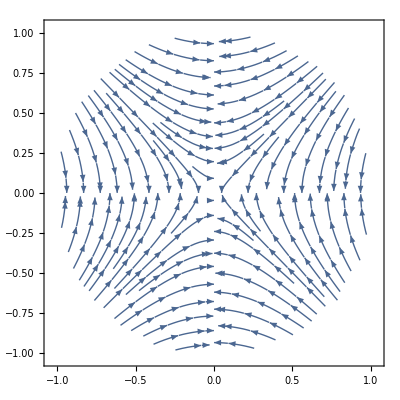

```mathematica
StreamPlot[
{-1/2 π y Sin[π x y],-1/2 π x Sin[π x y]},
{x,y}∈Disk[]]
```

```mathematica
Plot3D[(1+Cos[x y π])/2,{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Grad[(1+Cos[x y π])/2, {x,y}]
```

{-1/2 π y Sin[π x y],-1/2 π x Sin[π x y]}

```mathematica
StreamPlot[
{-1/2 π y Sin[π x y],-1/2 π x Sin[π x y]},
{x,y}∈Disk[]]
```

-Graphics-

```mathematica
Laplacian[(1+Cos[x y π])/2,{x,y}]
```

-1/2 π^2 x^2 Cos[π x y]-1/2 π^2 y^2 Cos[π x y]

```mathematica
Plot3D[-1/2 π^2 x^2 Cos[π x y]-1/2 π^2 y^2 Cos[π x y],{x,1105.3876457408633,1292.5068252690548},{y,-9.94311238963676,54.50922424212184}]
```

-Graphics3D-

```mathematica
Plot3D[-1/2 π^2 x^2 Cos[π x y]-1/2 π^2 y^2 Cos[π x y],{x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[-1/2 π^2 x^2 Cos[π x y]-1/2 π^2 y^2 Cos[π x y],{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
FullSimplify[
x (1+1/2 (-1-Cos[π x]))+x (1+Cos[π x]),
x∈Reals]
```

1/2 x (3+Cos[π x])

```mathematica
TrigReduce[1/2 x (3+Cos[π x])]
```

1/2 (3 x+x Cos[π x])

```mathematica
1/2 x (3+Cos[π x])
```

1/2 x (3+Cos[π x])

```mathematica
Plot[1/2 x (3+Cos[π x]),{x,-24.,24.}]
```

-Graphics-

```mathematica
D[u[x,t],t]==Laplacian[u[x,t],{x}]
```

u^(0,1)[x,t]==u^(2,0)[x,t]

```mathematica
1/2 x (3+Cos[π x])
```

```mathematica
{D[u[x,t],t]==Laplacian[u[x,t],{x}], u[x,0]==1/2 x (3+Cos[π x])}
```

{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==1/2 x (3+Cos[π x])}

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==1/2 x (3+Cos[π x])},{u[x,t],u[x,t]},{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==1/2 x (3+Cos[π x])},{u[x,t],u[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==1/2 x (3+Cos[π x])},{u[x,t]},{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==1/2 x (3+Cos[π x])},{u[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==Exp[x]},{u[x,t]},{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==ⅇ^x},{u[x,t]},{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},{u[x,t]},{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==x},{u[x,t]},{t,x}]

```mathematica
DSolveValue[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},{u[x,t]},{t,x}]
```

DSolveValue[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==x},{u[x,t]},{t,x}]

```mathematica
DSolveValue[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},u[x,t],{t,x}]
```

DSolveValue[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==x},u[x,t],{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},u[x,t],{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==x},u[x,t],{t,x}]

```mathematica
sol=DSolveValue[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},u[x,t],{x,t}]
```

x

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},u[x,t],{t,x}]
```

DSolve[{u^(0,1)[x,t]==u^(2,0)[x,t],u[x,0]==x},u[x,t],{t,x}]

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==x},u[x,t],{x,t}]
```

{{u[x,t]→x}}

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==Exp[x]},u[x,t],{x,t}]
```

{{u[x,t]→ⅇ^(t+x)}}

```mathematica
{{u[x,t]->ⅇ^(t+x)}}⟦1,1,2⟧
```

ⅇ^(t+x)

```mathematica
Plot3D[ⅇ^(t+x),{t,-5.895879734614027,5.895879734614027},{x,-5.895879734614027,5.895879734614027}]
```

-Graphics3D-

```mathematica
DSolve[{Derivative[0,1][u][x,t]==Derivative[2,0][u][x,t],u[x,0]==(1+Cos[π x])/2},u[x,t],{x,t}]
```

{{u[x,t]→1/2 (1+ⅇ^(-π^2 t) Cos[π x])}}

```mathematica
{{u[x,t]->1/2 (1+ⅇ^(-π^2 t) Cos[π x])}}⟦1,1,2⟧
```

1/2 (1+ⅇ^(-π^2 t) Cos[π x])

```mathematica
Plot3D[1/2 (1+ⅇ^(-π^2 t) Cos[π x]),{t,-7.687639203842082,7.687639203842082},{x,-2.,1.9999999999999998}]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (1+ⅇ^(-π^2 t) Cos[π x]),{t,0,3},{x,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (1+ⅇ^(-π^2 t) Cos[π x]),{t,0,3},{x,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[1/2 (1+ⅇ^(-π^2 t) Cos[π x]),{t,0,1.5},{x,-1,1}]
```

-Graphics3D-

```mathematica
(a-b)^2
```

(a-b)^2

```mathematica
Plot3D[(a-b)^2,{a,-5.707106781186548,5.707106781186548},{b,-5.707106781186548,5.707106781186548}]
```

-Graphics3D-

```mathematica
Laplacian[(x-y)^2, {x,y}]
```

4

```mathematica
Grad[(x,y)^2, {x,y}]
```

```mathematica
Grad[(x,y)^2, {x,y}]
```

```mathematica
1+1
```

2

```mathematica
3+3
```

6

```mathematica
Grad[(x,y)^2, {x,y}]
```

```mathematica
Div[(x,y)^2, {x,y}]
```

```mathematica
Grad[(x-y)^2, {x,y}]
```

{2 (x-y),-2 (x-y)}

```mathematica
Solve[{2 (x-y)==0,-2 (x-y)==0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→x}}

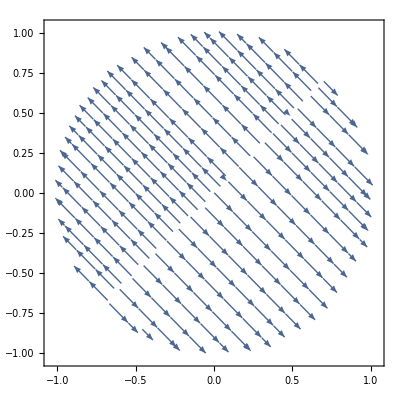

```mathematica
StreamPlot[
{2 (x-y),-2 (x-y)},
{x,y}∈Disk[]]
```

```mathematica
Plot3D[(a-b)^2,{a,b}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[(a-b)^2,{a,b}∈Disk[], AxesLabel->{a,b}]
```

-Graphics3D-

```mathematica
StreamPlot[
{2 (x-y),-2 (x-y)},
{x,y}∈Disk[]]
```

```mathematica
VectorPlot3D[
{2 (x-y),-2 (x-y)},
{x,y,z}∈Sphere[]]
```

VectorPlot3D::idomdim: {x,y,z}∈Sphere[] does not have a valid dimension as a plotting domain.

VectorPlot3D[{2 (x-y),-2 (x-y)},{x,y,z}∈Sphere[]]

```mathematica
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[]]
```

-Graphics3D-

```mathematica
VectorPlot3D[
{2 (x-y),-2 (x-y)},
{x,y,z}∈Cylinder[]]
```

VectorPlot3D::pllim: Range specification {x,y,z}∈Cylinder[] is not of the form {x, xmin, xmax}.

VectorPlot3D[{2 (x-y),-2 (x-y)},{x,y,z}∈Cylinder[]]

```mathematica
With[{l=1},
VectorPlot3D[
{2 (x-y),-2 (x-y), 0},
{x,-l,l},{y,-l,l},{z,-l,l}]]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[(a-b)^2,{a,b}∈Disk[], AxesLabel->{a,b}],
VectorPlot3D[
{2 (x-y),-2 (x-y), 0},
{x,-1,1},{y,-1,1},{z,-1,1}]}]
```

-Graphics3D-

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1},RegionFunction->((#1 #2 #3>0)&)]
```

-Graphics3D-

```mathematica
VectorPlot3D[
{2 (x-y),-2 (x-y), x},
{x,-1,1},{y,-1,1},{z,-1,1},
RegionFunction->((z==0)&)]
```

VectorPlot3D::invregion: z==0& must be a Boolean function.

-Graphics3D-

```mathematica
VectorPlot3D[{x,-y,z},{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,VectorScale->{Automatic,Scaled[0.4]},VectorStyle->Graphics3D[Sphere[{0,0,0},0.3]]]
```

-Graphics3D-

```mathematica
scalarField=x^2-y^2-z;
```

```mathematica
vectorField=D[scalarField,{{x,y,z}}]
```

{2 x,-2 y,-1}

```mathematica
v=VectorPlot3D[vectorField,{x,-2,2},{y,-2,2},{z,-2,2},VectorPoints->25,VectorScale->{0.1,Scaled[0.5]},RegionFunction->Function[{x,y,z},-0.1≤scalarField≤0.1]]
```

-Graphics3D-

```mathematica
c=ContourPlot3D[scalarField==0,{x,-2,2},{y,-2,2},{z,-2,2},Mesh->None,ContourStyle->Opacity[0.5,Green]]
```

-Graphics3D-

```mathematica
Show[v,c]
```

-Graphics3D-

```mathematica
g=VectorPlot3D[{Sin[x],Sin[y]^2,Cos[z]^3-Sin[x]},{x,-6,6},{y,-6,6},{z,-6,6},VectorStyle->"Arrow3D",VectorPoints->25,VectorColorFunction->"TemperatureMap",VectorScale->{0.1,Scaled[0.5]},RegionFunction->Function[{x,y,z},4^2<x^2+y^2+z^2<5^2]]
```

-Graphics3D-

```mathematica
VectorPlot3D[
{2 (x-y),-2 (x-y), x},
{x,-1,1},{y,-1,1},{z,-1,1},
RegionFunction->Function[{x,y,z},z==0]]
```

-Graphics3D-

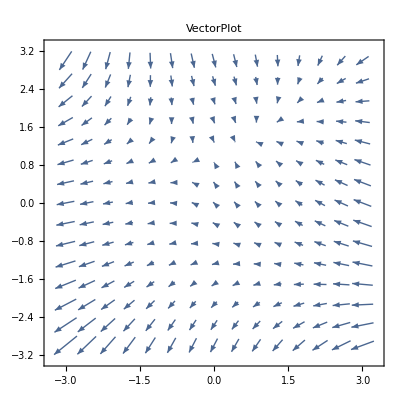
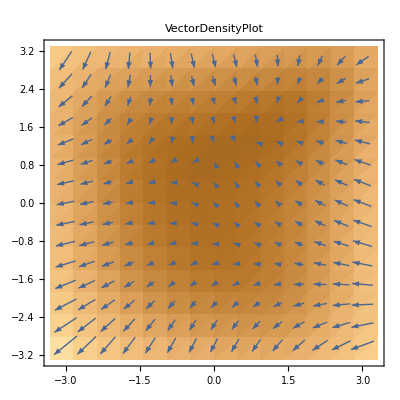
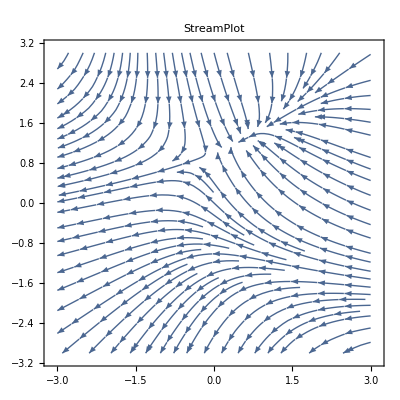
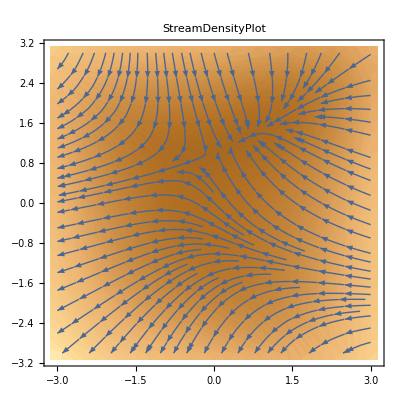
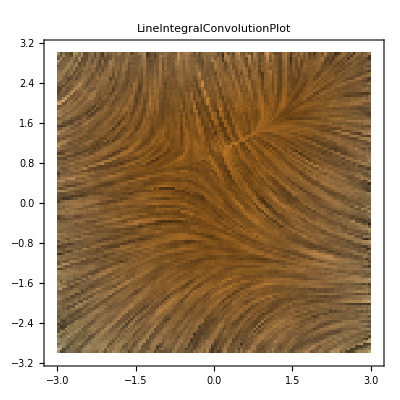

```mathematica
Table[f[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},PlotLabel->f],{f,{VectorPlot,VectorDensityPlot,StreamPlot,StreamDensityPlot,LineIntegralConvolutionPlot}}]
```

```mathematica
Quantity[5, "Minutes"]
```

5 min

```mathematica
FullForm[Quantity[5, "Minutes"]]
```

Quantity[5,"Minutes"]

```mathematica
180 Quantity[5,"Minutes"]
```

900 min

```mathematica
Quantity[5, "Minutes"]Quantity[180, IndependentUnit["beats"]/("Minutes")]
```

900 beats

```mathematica
LinguisticAssistant
```

```mathematica
Quantity[60,"Minutes"] Quantity[130,"Beats"]/Quantity[1, "Minutes"]
```

Quantity::timeout: A network operation for Quantity timed out. Please try again later.

Quantity::unkunit: Unable to interpret unit specification Beats.

60 Quantity[130,Beats]

```mathematica
130 60
```

7800

```mathematica
7800/900
```

26/3

```mathematica
N[26/3]
```

8.66667

```mathematica
5 26/3
```

130/3

```mathematica
N[130/3]
```

43.3333

```mathematica
Laplacian[f[x,y], {x,y}]==λ f[x,y]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]

```mathematica
<|"lol"->1|>
```

<|lol→1|>

```mathematica
<|"lol"->1|>["lol"]
```

1

```mathematica
CountryData[]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

{Entity[Country,Afghanistan],Entity[Country,AlandIslands],Entity[Country,Albania],Entity[Country,Algeria],Entity[Country,AmericanSamoa],Entity[Country,Andorra],Entity[Country,Angola],Entity[Country,Anguilla],Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
CountryData["UnitedStates", "ExportCommodities"]
```

{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts}

```mathematica
Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},Missing[NotAvailable],{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},Missing[NotAvailable],{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},Missing[NotAvailable],{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},Missing[NotAvailable],{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},Missing[NotAvailable],{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},Missing[NotAvailable],{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Fish},{Cotton,Gold,Livestock},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},Missing[NotAvailable],{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},Missing[NotAvailable],{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Phosphates},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},Missing[NotAvailable],{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},Missing[NotAvailable],{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Oil},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},Missing[NotAvailable],{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},Missing[NotAvailable],{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},Missing[NotAvailable],{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},Missing[NotAvailable],{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},Missing[NotAvailable],{Oil},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},Missing[NotAvailable],{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Phosphates},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
DeleteDuplicates@Join[Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},Missing[NotAvailable],{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
Join[Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},Missing[NotAvailable],{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},Missing[NotAvailable],{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},Missing[NotAvailable],{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},Missing[NotAvailable],{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},Missing[NotAvailable],{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},Missing[NotAvailable],{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Fish},{Cotton,Gold,Livestock},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},Missing[NotAvailable],{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},Missing[NotAvailable],{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Phosphates},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},Missing[NotAvailable],{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},Missing[NotAvailable],{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Oil},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},Missing[NotAvailable],{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},Missing[NotAvailable],{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},Missing[NotAvailable],{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},Missing[NotAvailable],{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},Missing[NotAvailable],{Oil},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},Missing[NotAvailable],{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Phosphates},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
DeleteMissing[
Join[Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Fish},{Cotton,Gold,Livestock},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Phosphates},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Oil},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},{Oil},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Phosphates},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},Missing[NotAvailable],{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},Missing[NotAvailable],{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},Missing[NotAvailable],{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},Missing[NotAvailable],{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},Missing[NotAvailable],{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},Missing[NotAvailable],{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Fish},{Cotton,Gold,Livestock},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},Missing[NotAvailable],{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},Missing[NotAvailable],{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Phosphates},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},Missing[NotAvailable],{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},Missing[NotAvailable],{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Oil},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},Missing[NotAvailable],{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},Missing[NotAvailable],{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},Missing[NotAvailable],{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},Missing[NotAvailable],{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},Missing[NotAvailable],{Oil},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},Missing[NotAvailable],{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Phosphates},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
DeleteMissing[
Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]]
```

{{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool},{Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables},{NaturalGas,Oil},{Seafood},{Furniture,Tobacco},{Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood},{Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood},{CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment},{Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts},{Copper,Diamonds,Energy,Food,Iron,Metals,Minerals},{AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment},{Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool},{Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles},{Cotton,Food,Machinery,NaturalGas,Oil},{AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables},{Aluminum,Oil,Textiles},{Fish,Jute,Leather,Seafood},{Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar},{Chemicals,Food,Machinery,Metals,Minerals,Textiles},{Chemicals,Diamonds,Food,Machinery,Metals},{Clothing,Fish,Fruit,Molasses,Sugar,Wood},{ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles},{Pharmaceuticals},{BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood},{NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc},{Clothing,Metals,Wood},{Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles},{Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment},{Beverages,BuildingMaterials,Fish,Fruit,Livestock},{Clothing,NaturalGas,Oil},{Clothing,Fuel,Iron,Machinery,Metals,Shoes},{Cotton,Gold,Livestock},{Coffee,Cotton,Leather,Sugar,Tea},{Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood},{Aluminum,Cocoa,Coffee,Cotton,Oil,Wood},{Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood},{Fish,Fuel,Leather,Shoes},{ConsumerGoods,TurtleProducts},{Coffee,Cotton,Diamonds,Tobacco,Wood},{Cotton,GumArabic,Livestock,Oil},{Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine},{Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles},{Phosphates},{CoconutProducts},{Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil},{CoconutProducts,PerfumeEssences,Spices},{Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells},{Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar},{Chemicals,Food,Fuel,Textiles,TransportationEquipment},{Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco},{BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops},{Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment},{Cobalt,Coffee,Copper,Diamonds,Oil},{Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills},{Coffee,Leather,LightIndustrial},{Fruit,Oil,Soap,Vegetables},{Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco},{BuildingMaterials,Coffee,PerfumeEssences,Spices},{Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood},{Chemicals,Cotton,Metals,Oil,Textiles},{Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles},{Cocoa,Methanol,Oil,Wood},{Food,Livestock,ManufacturedGoods,Sorghum,Textiles},{Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood},{Coffee,EdibleOils,Gold,Leather,Livestock,Qat},{Leather,Meat,Seafood,Wool},{Fish,ShipBuilding,Stamps},{CoconutProducts,Fish,Gold,Molasses,Sugar,Wood},{Chemicals,Machinery,Metals,Paper,Pulp,Wood},{Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment},{Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood},{CoconutProducts,Fish,Pearls,Shells,Spices},{Manganese,Oil,Uranium,Wood},{Cotton,Fish,LightIndustrial,Nuts,PalmProducts},{Flowers,Fruit,Textiles},{Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine},{Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles},{Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood},{ManufacturedGoods,Oil},{Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles},{Fish},{Clothing,Cocoa,Fruit,Mace,Spices,Vegetables},{Beverages,Fruit,SpringWater,Sugar},{Beverages,BuildingMaterials,Fish,Food,OilServices},{Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables},{Flowers,Vegetables},{AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold},{Nuts,PalmProducts,Seafood,Wood},{Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood},{Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods},{Coffee,EdibleOils,Fruit,Gold,Seafood,Wood},{Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches},{ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials},{Aluminum,AnimalProducts,Diatomite,Fish,Silicon},{Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles},{Appliances,NaturalGas,Oil,Rubber,Textiles,Wood},{Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals},{Oil},{AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals},{Fish,Lamb,Meat,Seafood,Textiles},{AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles},{Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment},{Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood},{Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar},{Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment},{Electronics,Food,LightIndustrial,Livestock,Textiles},{Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables},{Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool},{BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea},{CoconutProducts,Fish,Seaweed},{Appliances,Leather,Machinery,Metals},{Fertilizer,Oil},{Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool},{Coffee,Copper,ElectricPower,Gold,Tin,Wood},{Food,Machinery,Metals,Textiles,Wood},{BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables},{Food,Livestock,ManufacturedGoods,Textiles,Wool},{Cocoa,Coffee,Diamonds,Iron,Rubber,Wood},{Chemicals,NaturalGas,Oil},{DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts},{Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood},{Chemicals,Glass,Machinery,Metals,Rubber},{Clothing,Electronics,Machinery,Shoes,Textiles,Toys},{Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco},{Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles},{Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood},{Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood},{Fish},{Cotton,Gold,Livestock},{Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,CraftItems,Fish},{Beverages,Fruit,Oil},{Fish,Gold,Iron},{Clothing,Flowers,Molasses,Seafood,Sugar,Textiles},{CoconutProducts,Coffee,PerfumeEssences,Spices},{Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables},{Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices},{Food,Machinery,Textiles},{AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool},{Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices},{Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables},{Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood},{Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood},{Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc},{Phosphates},{Carpets,Cereals,Clothing,Jute,Leather},{Chemicals,Food,Fuel,Machinery},{Fish,Metals,Nickel},{Dairy,Fish,Machinery,Meat,Wood},{Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco},{Beans,Livestock,Uranium,Vegetables},{Cocoa,Oil,Rubber},{CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps},{Fruit,Nuts,PalmProducts,Stamps},{Textiles},{AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles},{Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding},{Fish,LightIndustrial,Metals,Oil,Textiles},{Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles},{CoconutProducts,Fish,Seafood},{Clothing,Coffee,Fruit,Seafood,Sugar},{Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood},{AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood},{Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc},{CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment},{CraftItems,Fruit,Stamps,Vegetables},{Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood},{Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood},{Fertilizer,Metals,NaturalGas,Oil},{Cocoa,Coffee,Diamonds,Oil,Sugar,Wood},{Beverages,Molasses,PerfumeEssences,Seafood,Sugar},{AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles},{Armaments,Chemicals,Metals,NaturalGas,Oil,Wood},{Coffee,Leather,Tea,Tin},{Coffee,CraftItems,Fish},{Beverages,Electronics,Food,Machinery,Tobacco},{Clothing,Cocoa,CoconutProducts,Fruit,Vegetables},{AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans},{Fruit,RootCrops,SportsGoods},{Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables},{BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood},{Cocoa,CoconutProducts,Coffee,EdibleOils},{Oil},{Cotton,Fish,Nuts,Oil,Phosphates},{Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment},{CoconutProducts,Fish,Oil,Seafood,Spices},{Cocoa,Coffee,Diamonds,Fish,Titanium},{Chemicals,ConsumerGoods,Fuel,Machinery},{Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics},{Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment},{Cocoa,CoconutProducts,EdibleOils,Fish,Wood},{Charcoal,Fish,Fruit,Leather,Livestock,Metals},{Diamonds,Gold,Machinery,Metals,Minerals,Platinum},{Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding},{Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals},{Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles},{Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar},{Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood},{Appliances,Beverages,Fruit,Sugar,Textiles,Wood},{Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood},{AgriculturalProducts,Chemicals,Machinery,Metals,Watches},{Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables},{Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles},{Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles},{Coffee,Cotton,Gold,ManufacturedGoods,Nuts},{Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles},{Cocoa,Coffee,Cotton,Phosphates},{CoconutProducts,CraftItems,Stamps},{Fish,RootCrops,Spices,Vegetables},{Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables},{AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles},{Clothing,Food,Metals,Textiles,TransportationEquipment},{NaturalGas,Oil,Petrochemicals,Textiles},{Seafood,Shells},{CoconutProducts,Fish},{Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea},{Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment},{Dates,Fish,NaturalGas,Oil},{Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco},{AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts},{Oil},{Dairy,Fish,Leather,Meat,Rice,Wool},{Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles},{Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood},{AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil},{Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea},{BuildingMaterials,Chemicals,CoconutProducts},{EdibleOils,Fruit,Limestone,Vegetables},{Phosphates},{Coffee,Fish,Oil},{Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco},{Cotton,Gold,Metals,Platinum,Textiles,Tobacco}}

```mathematica
Flatten[
DeleteMissing[
Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]],1]
```

{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool,Asphalt,Fruit,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables,NaturalGas,Oil,Seafood,Furniture,Tobacco,Coffee,Cotton,Diamonds,Fish,NaturalGas,Oil,Sisal,Wood,Beverages,BuildingMaterials,Fish,Livestock,Salt,Seafood,CraftItems,ElectricalComponents,Food,Furniture,Livestock,Oil,TransportationEquipment,Automobiles,Cereals,NaturalGas,Oil,Soybeans,SoyProducts,Copper,Diamonds,Energy,Food,Iron,Metals,Minerals,AnimalProducts,Art,CraftItems,ElectricalEquipment,Livestock,Machinery,TransportationEquipment,Aluminum,Cereals,Coal,Gold,Iron,Machinery,Meat,TransportationEquipment,Wool,Automobiles,Chemicals,Food,Iron,Machinery,Metals,Paper,Textiles,Cotton,Food,Machinery,NaturalGas,Oil,AnimalProducts,Beverages,Chemicals,Fruit,Minerals,Salt,Vegetables,Aluminum,Oil,Textiles,Fish,Jute,Leather,Seafood,Beverages,Chemicals,ElectricalComponents,Food,ManufacturedGoods,Molasses,Sugar,Chemicals,Food,Machinery,Metals,Minerals,Textiles,Chemicals,Diamonds,Food,Machinery,Metals,Clothing,Fish,Fruit,Molasses,Sugar,Wood,ConsumerGoods,Cotton,Nuts,PalmProducts,Seafood,Textiles,Pharmaceuticals,BuildingMaterials,CraftItems,ElectricPower,Fruit,Gems,Gypsum,Spices,Wood,NaturalGas,Oil,Soybeans,SoyProducts,Tin,Zinc,Clothing,Metals,Wood,Copper,Diamonds,Meat,Nickel,SodaAsh,Textiles,Automobiles,Coffee,Iron,Shoes,Soybeans,TransportationEquipment,Beverages,BuildingMaterials,Fish,Fruit,Livestock,Clothing,NaturalGas,Oil,Clothing,Fuel,Iron,Machinery,Metals,Shoes,Cotton,Gold,Livestock,Coffee,Cotton,Leather,Sugar,Tea,Clothing,Fish,Rice,Rubber,Shoes,Tobacco,Wood,Aluminum,Cocoa,Coffee,Cotton,Oil,Wood,Aircraft,Aluminum,Automobiles,Chemicals,CommunicationsEquipment,ElectricPower,Fertilizer,IndustrialEquipment,NaturalGas,Oil,Plastics,Wood,Fish,Fuel,Leather,Shoes,ConsumerGoods,TurtleProducts,Coffee,Cotton,Diamonds,Tobacco,Wood,Cotton,GumArabic,Livestock,Oil,Chemicals,Copper,Fish,Fruit,Paper,Pulp,Wine,Clothing,Computers,CommunicationsEquipment,Electronics,Machinery,Steel,Textiles,Phosphates,CoconutProducts,Clothing,Coal,Coffee,Flowers,Fruit,Gems,Nickel,Oil,CoconutProducts,PerfumeEssences,Spices,Clothing,CoconutProducts,Coffee,Fish,Fruit,Pearls,Shells,Coffee,ConsumerGoods,Electronics,Fruit,MedicalEquipment,Seafood,Sugar,Chemicals,Food,Fuel,Textiles,TransportationEquipment,Coffee,Fish,Fruit,MedicalSupplies,Nickel,Sugar,Tobacco,BuildingMaterials,Clothing,Fruit,Pharmaceuticals,RootCrops,Chemicals,Fuel,Machinery,RawMaterials,TransportationEquipment,Cobalt,Coffee,Copper,Diamonds,Oil,Dairy,Fish,Furniture,Instruments,Machinery,Meat,Pharmaceuticals,Windmills,Coffee,Leather,LightIndustrial,Fruit,Oil,Soap,Vegetables,Cocoa,Coffee,ConsumerGoods,Gold,Meat,Metals,Silver,Sugar,Tobacco,BuildingMaterials,Coffee,PerfumeEssences,Spices,Cocoa,Coffee,Fish,Flowers,Fruit,HorticulturalProducts,Oil,Seafood,Wood,Chemicals,Cotton,Metals,Oil,Textiles,Chemicals,Coffee,ElectricPower,LightIndustrial,Seafood,Sugar,Textiles,Cocoa,Methanol,Oil,Wood,Food,Livestock,ManufacturedGoods,Sorghum,Textiles,Chemicals,Food,Furniture,Machinery,Metals,Paper,Textiles,Wood,Coffee,EdibleOils,Gold,Leather,Livestock,Qat,Leather,Meat,Seafood,Wool,Fish,ShipBuilding,Stamps,CoconutProducts,Fish,Gold,Molasses,Sugar,Wood,Chemicals,Machinery,Metals,Paper,Pulp,Wood,Aircraft,Beverages,Chemicals,Iron,Machinery,Metals,Pharmaceuticals,Plastics,TransportationEquipment,Beverages,Clothing,Gold,PerfumeEssences,Seafood,Wood,CoconutProducts,Fish,Pearls,Shells,Spices,Manganese,Oil,Uranium,Wood,Cotton,Fish,LightIndustrial,Nuts,PalmProducts,Flowers,Fruit,Textiles,Automobiles,Beverages,ConsumerGoods,Fruit,Metals,Nuts,RawMaterials,Wine,Automobiles,Chemicals,Food,Machinery,ManufacturedGoods,Metals,Textiles,Aluminum,Cocoa,Diamonds,Fish,Gold,HorticulturalProducts,Manganese,Wood,ManufacturedGoods,Oil,Beverages,Chemicals,Food,ManufacturedGoods,Oil,Textiles,Fish,Clothing,Cocoa,Fruit,Mace,Spices,Vegetables,Beverages,Fruit,SpringWater,Sugar,Beverages,BuildingMaterials,Fish,Food,OilServices,Clothing,Coffee,Fruit,Oil,Spices,Sugar,Vegetables,Flowers,Vegetables,AgriculturalProducts,Aluminum,Coffee,Diamonds,Fish,Gold,Nuts,PalmProducts,Seafood,Wood,Aluminum,Beverages,Gold,Molasses,Rice,Seafood,Sugar,Wood,Clothing,Cocoa,Coffee,EdibleOils,Fruit,ManufacturedGoods,Coffee,EdibleOils,Fruit,Gold,Seafood,Wood,Appliances,Clocks,Clothing,ElectricalEquipment,Gems,Plastics,Publishing,Shoes,Textiles,Toys,Watches,ElectricPower,Food,Fuel,Machinery,ManufacturedGoods,RawMaterials,Aluminum,AnimalProducts,Diatomite,Fish,Silicon,Chemicals,Engineering,Gems,Jewelry,Leather,Oil,Textiles,Appliances,NaturalGas,Oil,Rubber,Textiles,Wood,Carpets,Chemicals,Fruit,Nuts,Oil,Petrochemicals,Oil,AnimalProducts,Chemicals,Computers,Livestock,Machinery,Pharmaceuticals,Fish,Lamb,Meat,Seafood,Textiles,AgriculturalProducts,Chemicals,Clothing,Diamonds,Machinery,Software,Textiles,Automobiles,Beverages,Chemicals,Clothing,Engineering,Food,IndustrialEquipment,Metals,Minerals,Textiles,Tobacco,TransportationEquipment,Cocoa,Coffee,Cotton,EdibleOils,Fish,Fruit,Oil,Wood,Aluminum,Beverages,Chemicals,Clothing,Coffee,Fruit,Fuel,RootCrops,Sugar,Automobiles,Chemicals,ElectricalEquipment,Semiconductors,TransportationEquipment,Electronics,Food,LightIndustrial,Livestock,Textiles,Clothing,Fertilizer,ManufacturedGoods,Pharmaceuticals,Phosphates,Potash,Vegetables,Cereals,Chemicals,Coal,Machinery,Meat,Metals,Oil,Wool,BuildingMaterials,Coffee,Fish,HorticulturalProducts,Oil,Tea,CoconutProducts,Fish,Seaweed,Appliances,Leather,Machinery,Metals,Fertilizer,Oil,Cotton,ElectricPower,Gold,Machinery,Meat,Mercury,NaturalGas,Shoes,Tobacco,Uranium,Wool,Coffee,Copper,ElectricPower,Gold,Tin,Wood,Food,Machinery,Metals,Textiles,Wood,BuildingMaterials,Chemicals,ConsumerGoods,ElectricalEquipment,Fruit,Jewelry,Paper,Switchgear,Textiles,Tobacco,Vegetables,Food,Livestock,ManufacturedGoods,Textiles,Wool,Cocoa,Coffee,Diamonds,Iron,Rubber,Wood,Chemicals,NaturalGas,Oil,DentalProducts,ElectricalComponents,Electronics,Food,Hardware,Machinery,OpticalEquipment,VehicleParts,Chemicals,Clothing,Food,Machinery,Minerals,Textiles,Wood,Chemicals,Glass,Machinery,Metals,Rubber,Clothing,Electronics,Machinery,Shoes,Textiles,Toys,Beverages,Food,Iron,ManufacturedGoods,Metals,Steel,Textiles,Tobacco,Chromite,Coffee,Oil,Seafood,Spices,Sugar,Textiles,Clothing,Coffee,Cotton,Nuts,Sugar,Tea,Tobacco,Wood,Chemicals,EdibleOils,Electronics,NaturalGas,Oil,Rubber,Textiles,Wood,Fish,Cotton,Gold,Livestock,Machinery,ManufacturedGoods,TransportationEquipment,CoconutProducts,CraftItems,Fish,Beverages,Fruit,Oil,Fish,Gold,Iron,Clothing,Flowers,Molasses,Seafood,Sugar,Textiles,CoconutProducts,Coffee,PerfumeEssences,Spices,Coffee,Cotton,Fruit,ManufacturedGoods,Oil,Silver,Vegetables,Clothing,ConsumerGoods,Fish,Fruit,HorticulturalProducts,Spices,Food,Machinery,Textiles,AnimalProducts,Clothing,Copper,Fluorspar,Leather,Livestock,Metals,Wool,Clothing,Electronics,Fruit,HorticulturalProducts,Livestock,Plastics,Spices,Chemicals,Clothing,ElectricalComponents,Fertilizer,Fish,Fruit,Minerals,Oil,Textiles,Vegetables,Aluminum,Cotton,Electricity,Fruit,Nuts,Seafood,Sugar,Wood,Beans,Clothing,ConsumerGoods,Fish,Gems,NaturalGas,Pulses,Rice,Wood,Copper,Diamonds,Fish,Gold,Livestock,Metals,Skins,Uranium,Zinc,Phosphates,Carpets,Cereals,Clothing,Jute,Leather,Chemicals,Food,Fuel,Machinery,Fish,Metals,Nickel,Dairy,Fish,Machinery,Meat,Wood,Coffee,Gold,Meat,Nuts,Seafood,Sugar,Tobacco,Beans,Livestock,Uranium,Vegetables,Cocoa,Oil,Rubber,CoconutProducts,CraftItems,Footballs,Fruit,Honey,RootCrops,Spices,Stamps,Fruit,Nuts,PalmProducts,Stamps,Textiles,AgriculturalProducts,Fish,ManufacturedGoods,Metals,Minerals,Textiles,Chemicals,Fish,Machinery,Metals,Oil,ShipBuilding,Fish,LightIndustrial,Metals,Oil,Textiles,Carpets,Chemicals,Leather,ManufacturedGoods,Rice,SportsGoods,Textiles,CoconutProducts,Fish,Seafood,Clothing,Coffee,Fruit,Seafood,Sugar,Cocoa,Coffee,Copper,EdibleOils,Gold,Oil,Seafood,Wood,AnimalFeed,Cotton,EdibleOils,ElectricPower,Leather,Meat,Soybeans,Wood,Coffee,ConsumerGoods,Copper,Gold,Oil,RootCrops,Textiles,Vegetables,Zinc,CoconutProducts,Copper,Electronics,Fruit,Oil,Semiconductors,TransportationEquipment,CraftItems,Fruit,Stamps,Vegetables,Food,IndustrialProducts,Livestock,Machinery,ManufacturedGoods,TransportationEquipment,AgriculturalProducts,Automobiles,Chemicals,Clothing,Cork,Food,Leather,Machinery,MedicalEquipment,Metals,Minerals,Machinery,Oil,OpticalEquipment,Plastics,Paper,Rubber,Shoes,Skins,Textiles,TransportationEquipment,Wood,Beverages,Chemicals,Clothing,Electronics,MedicalEquipment,Seafood,Fertilizer,Metals,NaturalGas,Oil,Cocoa,Coffee,Diamonds,Oil,Sugar,Wood,Beverages,Molasses,PerfumeEssences,Seafood,Sugar,AgriculturalProducts,Chemicals,Fuel,Machinery,Metals,Minerals,Shoes,Textiles,Armaments,Chemicals,Metals,NaturalGas,Oil,Wood,Coffee,Leather,Tea,Tin,Coffee,CraftItems,Fish,Beverages,Electronics,Food,Machinery,Tobacco,Clothing,Cocoa,CoconutProducts,Fruit,Vegetables,AnimalFeed,Fish,Fox,Furs,Seafood,Soybeans,Fruit,RootCrops,SportsGoods,Automobiles,Beverages,CoconutProducts,Dairy,Fish,Vegetables,BakedGoods,BuildingMaterials,Ceramics,Cereals,Leather,Lime,Nuts,Wine,Wood,Cocoa,CoconutProducts,Coffee,EdibleOils,Oil,Cotton,Fish,Nuts,Oil,Phosphates,Food,Livestock,Machinery,ManufacturedGoods,TransportationEquipment,CoconutProducts,Fish,Oil,Seafood,Spices,Cocoa,Coffee,Diamonds,Fish,Titanium,Chemicals,ConsumerGoods,Fuel,Machinery,Automobiles,Chemicals,ElectricalEquipment,Machinery,Metals,Minerals,Plastics,Chemicals,Food,Machinery,ManufacturedGoods,TransportationEquipment,Cocoa,CoconutProducts,EdibleOils,Fish,Wood,Charcoal,Fish,Fruit,Leather,Livestock,Metals,Diamonds,Gold,Machinery,Metals,Minerals,Platinum,Automobiles,CommunicationsEquipment,Computers,Metals,Petrochemicals,Semiconductors,ShipBuilding,Automobiles,ConsumerGoods,Food,Machinery,MedicalSupplies,Pharmaceuticals,Clothing,CoconutProducts,Diamonds,Fish,Gems,Rubber,Spices,Tea,Textiles,Cotton,EdibleOils,GumArabic,Livestock,Nuts,Oil,Sugar,Aluminum,Gold,Fish,Fruit,Oil,Rice,Seafood,Wood,Appliances,Beverages,Fruit,Sugar,Textiles,Wood,Automobiles,Chemicals,Iron,Machinery,Metals,Paper,Pulp,Wood,AgriculturalProducts,Chemicals,Machinery,Metals,Watches,Cereals,Clothing,Fruit,Livestock,Meat,Minerals,Oil,Textiles,Vegetables,Automobiles,Chemicals,Electronics,Metals,Plastics,Textiles,Aluminum,Cotton,EdibleOils,ElectricPower,Fruit,Textiles,Coffee,Cotton,Gold,ManufacturedGoods,Nuts,Appliances,Automobiles,Computers,Fish,Jewelry,Rice,Rubber,Shoes,Textiles,Cocoa,Coffee,Cotton,Phosphates,CoconutProducts,CraftItems,Stamps,Fish,RootCrops,Spices,Vegetables,Chemicals,Beverages,Cereals,Cocoa,Coffee,ConsumerGoods,Fertilizer,Flowers,Fruit,Metals,Methanol,NaturalGas,Oil,Sugar,Steel,Vegetables,AgriculturalProducts,Chemicals,Clothing,ConsumerGoods,Electronics,MechanicalGoods,NaturalGas,Oil,Phosphates,Textiles,Clothing,Food,Metals,Textiles,TransportationEquipment,NaturalGas,Oil,Petrochemicals,Textiles,Seafood,Shells,CoconutProducts,Fish,Coffee,Cotton,Fish,Flowers,Gold,HorticulturalProducts,Tea,Chemicals,Food,Fuel,Machinery,Metals,Oil,TransportationEquipment,Dates,Fish,NaturalGas,Oil,Beverages,Chemicals,Food,Fuel,ManufacturedGoods,Tobacco,AgriculturalProducts,Aircraft,Automobiles,Cereals,Chemicals,CommunicationsEquipment,Computers,Electronics,MedicalEquipment,MedicalSupplies,VehicleParts,Oil,Dairy,Fish,Leather,Meat,Rice,Wool,Automobiles,Cotton,Energy,Fertilizer,Food,Gold,Machinery,Metals,Textiles,Cocoa,CoconutProducts,Coffee,Kava,Meat,Wood,AgriculturalProducts,Aluminum,BasicManufactures,Chemicals,Metals,Oil,Coffee,MarineProducts,Oil,Rice,Rubber,Shoes,Tea,BuildingMaterials,Chemicals,CoconutProducts,EdibleOils,Fruit,Limestone,Vegetables,Phosphates,Coffee,Fish,Oil,Cobalt,Copper,Cotton,ElectricPower,Flowers,Tobacco,Cotton,Gold,Metals,Platinum,Textiles,Tobacco}

```mathematica
DeleteDuplicates[
Flatten[
DeleteMissing[
Map[
CountryData[#, "ExportCommodities"]&,
CountryData[]]],1]]
```

{Carpets,Cotton,Fruit,Furs,Gems,Leather,Nuts,Opium,Wool,Asphalt,Metals,Oil,Shoes,Textiles,Tobacco,Vegetables,NaturalGas,Seafood,Furniture,Coffee,Diamonds,Fish,Sisal,Wood,Beverages,BuildingMaterials,Livestock,Salt,CraftItems,ElectricalComponents,Food,TransportationEquipment,Automobiles,Cereals,Soybeans,SoyProducts,Copper,Energy,Iron,Minerals,AnimalProducts,Art,ElectricalEquipment,Machinery,Aluminum,Coal,Gold,Meat,Chemicals,Paper,Jute,ManufacturedGoods,Molasses,Sugar,Clothing,ConsumerGoods,PalmProducts,Pharmaceuticals,ElectricPower,Gypsum,Spices,Tin,Zinc,Nickel,SodaAsh,Fuel,Tea,Rice,Rubber,Cocoa,Aircraft,CommunicationsEquipment,Fertilizer,IndustrialEquipment,Plastics,TurtleProducts,GumArabic,Pulp,Wine,Computers,Electronics,Steel,Phosphates,CoconutProducts,Flowers,PerfumeEssences,Pearls,Shells,MedicalEquipment,MedicalSupplies,RootCrops,RawMaterials,Cobalt,Dairy,Instruments,Windmills,LightIndustrial,Soap,Silver,HorticulturalProducts,Methanol,Sorghum,EdibleOils,Qat,ShipBuilding,Stamps,Manganese,Uranium,Mace,SpringWater,OilServices,AgriculturalProducts,Appliances,Clocks,Publishing,Toys,Watches,Diatomite,Silicon,Engineering,Jewelry,Petrochemicals,Lamb,Software,Semiconductors,Potash,Seaweed,Mercury,Switchgear,DentalProducts,Hardware,OpticalEquipment,VehicleParts,Glass,Chromite,Fluorspar,Electricity,Beans,Pulses,Skins,Footballs,Honey,SportsGoods,AnimalFeed,IndustrialProducts,Cork,Armaments,Fox,BakedGoods,Ceramics,Lime,Titanium,Charcoal,Platinum,MechanicalGoods,Dates,Kava,BasicManufactures,MarineProducts,Limestone}

```mathematica
Length@Out@232
```

160

```mathematica
CountryData["UnitedStates", "NaturalResources"]
```

{bauxite,coal,copper,gold,iron,lead,mercury,molybdenum,natural gas,nickel,oil,phosphates,potash,silver,timber,tungsten,uranium,zinc}

```mathematica
"plot in world map""UnitedStates"Manipulate[Graphics[({EdgeForm[Brown],If[#1==="UnitedStates",Orange,LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{prop,"NaturalResources","country property"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

```mathematica
Div[f[x],x]
```

f[x]x

```mathematica
Grad[f[x],x]
```

f[x]x

```mathematica
∇_x^2 f[x]
```

f[x]x

```mathematica
D[f[x],x]-λ f[x]
```

-λ f[x]+f'[x]

```mathematica
Simplify[-λ f[x]+f'[x]]
```

-λ f[x]+f'[x]

```mathematica
Laplacian[f[x,y], {x,y}]==λ f[x]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x],{f[x,y],f[x,y]},{x,y}]
```

DSolve::dvlen: The function f[x] does not have the same number of arguments as independent variables (2).

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x],{f[x,y],f[x,y]},{x,y}]

```mathematica
-Laplacian[f[x,y], {x,y}]==λ f[x]
```

-f^(0,2)[x,y]-f^(2,0)[x,y]==λ f[x]

```mathematica
DSolve[-Derivative[0,2][f][x,y]-Derivative[2,0][f][x,y]==λ f[x],{f[x,y],f[x,y]},{x,y}]
```

DSolve::dvlen: The function f[x] does not have the same number of arguments as independent variables (2).

DSolve[-f^(0,2)[x,y]-f^(2,0)[x,y]==λ f[x],{f[x,y],f[x,y]},{x,y}]

```mathematica
Exp[f'[x]/f[x]]
```

ⅇ^(f'[x]/f[x])

```mathematica
With[{f=Identity},
ⅇ^(f'[x]/f[x])]
```

ⅇ^(1/x)

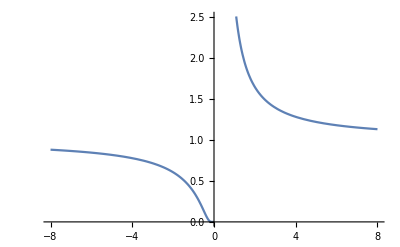

```mathematica
Plot[ⅇ^(1/x),{x,-8,8}]
```

```mathematica
1==∫_-a^a x^2 ⅆx
```

1==(2 a^3)/3

```mathematica
Reduce[1==(2 a^3)/3]
```

a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3)

```mathematica
(3/2)^(1/3)
```

(3/2)^(1/3)

```mathematica
N[(3/2)^(1/3)]
```

1.14471

```mathematica
∫_(-(3/2)^(1/3))^((3/2)^(1/3)) x^2 ⅆx
```

1